```mathematica
y[x_]:=-Exp[-a (x+L)]
```

```mathematica
k[En_]:=√(En^2-1);
ν [En_]:= (ⅈ k[En])/a;
μ[En_]:=(√(1-(En-V0)^2))/a;
λ[En_]:=(√(a^2-4 V0^2))/(2 a);
λ1[En_]:=-1/2+λ[En];
```

```mathematica
ϕL[x_,En_]:=D1 y[x]^μ[En] (1-y[x])^(-λ1[En]) Hypergeometric2F1[μ[En]-ν[En]-λ1[En],μ[En]+ν[En]-λ1[En],1+2 μ[En],y[x]]+ D2 y[x]^(-μ[En])(1-y[x])^(-λ1[En]) Hypergeometric2F1[-μ[En]-ν[En]-λ1[En],-μ[En]+ν[En]-λ1[En],1-2 μ[En],y[x]]
```

```mathematica
A[En_]:=D1 ((Gamma[1-2 μ[En]] Gamma[-2 ν[En]] (-1)^(-μ[En]))/(Gamma[-μ[En] - ν[En] -λ1[En]]Gamma[1-μ[En]-ν[En]+λ1[En]]))+D2 ((Gamma[1+2 μ[En]] Gamma[-2 ν[En]](-1)^μ[En])/(Gamma[μ[En]-ν[En]-λ1[En]] Gamma[1+μ[En]-ν[En]+λ1[En]]));
B[En_] :=D1 ((Gamma[1-2 μ[En]] Gamma[2 ν[En]] (-1)^(-μ[En]))/(Gamma[-μ[En] + ν[En] -λ1[En]]Gamma[1-μ[En]+ν[En]+λ1[En]]))+D2 ((Gamma[1+2 μ[En]] Gamma[2 ν[En]](-1)^μ[En])/(Gamma[μ[En]+ν[En]-λ1[En]] Gamma[1+μ[En]+ν[En]+λ1[En]]));
```

```mathematica
A1[En_]:=D1*(Gamma[1-2 μ[En]]*Gamma[-2 ν[En]]*Exp[-I Pi μ[En]])/(Gamma[-μ[En]-ν[En]-λ1[En]]*Gamma[1-μ[En]-ν[En]+λ1[En]])
+D2*(Gamma[1+2 μ[En]]*Gamma[-2 ν[En]]*Exp[+I Pi μ[En]])/(Gamma[μ[En]-ν[En]-λ1[En]]*Gamma[1+μ[En]-ν[En]+λ1[En]]);

B1[En_]:=D1*(Gamma[1-2 μ[En]]*Gamma[+2 ν[En]]*Exp[-I Pi μ[En]])/(Gamma[-μ[En]+ν[En]-λ1[En]]*Gamma[1-μ[En]+ν[En]+λ1[En]])
+D2*(Gamma[1+2 μ[En]]*Gamma[+2 ν[En]]*Exp[+I Pi μ[En]])/(Gamma[μ[En]+ν[En]-λ1[En]]*Gamma[1+μ[En]+ν[En]+λ1[En]]);
```

```mathematica
z[x_]:=1/(1+Exp[a(x-L)])
```

```mathematica
ϕR[x_,En_]:=d1 z[x]^(-ν[En])(1-z[x])^(-μ[En]) Hypergeometric2F1[1/2-ν[En]-μ[En]-λ[En],1/2-ν[En]-μ[En]+λ[En],1-2 ν[En],z[x]]
```

```mathematica
(*assume you already defined y[x],z[x],ϕL,ϕR,and A,B using Exp[±I Pi μ[En]]*)y0=y[0];z0=z[0];
dy0=D[y[x],x]/. x->0;   (*-a y0*)
dz0=D[z[x],x]/. x->0;   (*-a z0 (1-z0)*)

meq1[En_]:=(ϕL[0,En]==ϕR[0,En])/. {y[0]->y0,z[0]->z0};
meq2[En_]:=((D[ϕL[x,En],x]/. x->0)==(D[ϕR[x,En],x]/. x->0))/. {y[0]->y0,z[0]->z0,D[y[x],x]->dy0,D[z[x],x]->dz0};

sol12[En_,wp_:80]:=Solve[SetPrecision[{meq1[En],meq2[En]},wp],{D1,D2},WorkingPrecision->wp][[1]];
```

```mathematica
alphaBetaNum[aVal_,LVal_,V0Val_][En_?NumericQ]:=Module[{a=aVal,L=LVal,V0=V0Val,kE,s,x1,x2,g1,g2,M,rhs,Aover,Bover},kE=Sqrt[En^2-1];
s=sol12[En,80];(*D1,D2 in terms of d1*)(*choose two far-left points;-8/a and-10/a beyond-L work well*)x1=-L-8./a;x2=-L-10./a;
g1=(ϕL[x1,En]/. s)/d1;(* =(A e^{ik(x1+L)}+B e^{-ik(x1+L)})/d1*)
g2=(ϕL[x2,En]/. s)/d1;
M={{Exp[I kE (x1+L)],Exp[-I kE (x1+L)]},{Exp[I kE (x2+L)],Exp[-I kE (x2+L)]}};
rhs={g1,g2};
{Aover,Bover}=LinearSolve[N[M,80],N[rhs,80]];
{Aover,Bover} (* ={alpha,beta}*)];
```

```mathematica
Tnum[a_,L_,V0_][En_?NumericQ]:=Module[{α,β},{α,β}=alphaBetaNum[a,L,V0][En];
N[1/Abs[α]^2]];

Rnum[a_,L_,V0_][En_?NumericQ]:=Module[{α,β},{α,β}=alphaBetaNum[a,L,V0][En];
N[Abs[β/α]^2]];

unitarityCheck[aVal_,LVal_,V0Val_,En_]:=Module[{},{a,L,V0}=N@{aVal,LVal,V0Val};
With[{T=Tnum[a,L,V0][En],R=Rnum[a,L,V0][En]},{T,R,T+R}//N]];
```

```mathematica
unitarityCheck[2,2,4,2.5]
```

{0.341365,0.658371,0.999737}

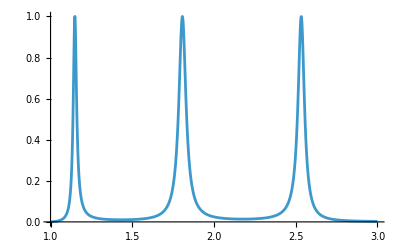

```mathematica
Plot[Tnum[2,2,4][En],{En,1,4-1},PlotRange->All]
```